1. Naj bo U = {1, 2, ..., 12} univerzalna množica. Podani so množice A = {1, 2, 4, 7, 9, 11}, B = {2, 4, 5, 8, 9, 12} in C={3, 7, 9, 10}.. Določi naslednje množice:

a) A ∪ B

Definirajmo množici A in B ter določimo njuno unijo :

```mathematica
A={1,2,4,7,9,11};
B={2,4,5,8,9,12};
Union[A,B]
```

{1,2,4,5,7,8,9,11,12}

b) A ∩ B

Podobno kot prej določimo presek množic :

```mathematica
Intersection[A,B]
```

{2,4,9}

c) A\B

Podobno kot prej določimo razliko množic:

```mathematica
Complement[A,B]
```

{1,7,11}

d) A^c

Določimo komplement množice A. To lahko določimo kot razliko med univerzalno množico, ki jo moramo najprej definirati, in množico A.

```mathematica
U=Range[12];
```

```mathematica
Complement[U,A]
```

{3,5,6,8,10,12}

e) A∩B^c

Podobno kot v prejšnjih primerih določimo zgornjo množico:

```mathematica
Intersection[A,Complement[U,B]]
```

{1,7,11}

f)(A∩B^c)∪C^c

Podobno kot v prejšnjih primerih določimo zgornjo množico, še prej pa definirajmo množico C (pri tem uporabimo malo črko, saj velika je zasedena):

```mathematica
c={3,7,9,10};
Union[Intersection[A,Complement[U,B]], Complement[U,c]]
```

{1,2,4,5,6,7,8,11,12}

3. Dana je funkcija f(x) = arctan ((ⅇ^x-ⅇ^-x)/(ⅇ^x+ⅇ^-x)).

a) Določi ničle funkcije f.

Definirajmo funkcijo f in izračunajmo njene ničle :

```mathematica
f[x_] := ArcTan[(E^(x)-E^(-x))/(E^x+E^(-x))]
```

```mathematica
f[x]
```

ArcTan[(-ⅇ^-x+ⅇ^x)/(ⅇ^-x+ⅇ^x)]

```mathematica
Solve[f[x]==0, x, Reals]
```

{{x→0}}

b) Določi definicijsko območje funkcije f.

Kot vidimo je funkcija f kompozitum krožne in racionalne funkcije z eksponentnimi spremenljivkami. Ker so racionalne funkcije definirane na celi množici ℝ razen v polih, poskusimo določiti pole :

```mathematica
Solve[Denominator[Tan[f[x]]]==0,x, Reals]
```

{}

Funkcija f torej nima polov in je definirana na celotni množici ℝ .

c) Dokaži, da je funkcija f liha.

Po definiciji je funkcija f liha natanko tedaj, ko velja f (-x) = -f (x) za vsak x definicijskega območja. Poskusimo v naši funkciji spremenljivko x nadomestiti z -x in funkcijo f(-x) poenostaviti:

```mathematica
f[x] /.x->-x
```

ArcTan[(ⅇ^-x-ⅇ^x)/(ⅇ^-x+ⅇ^x)]

V dobljeni funkciji, bi lahko v števcu argumenta krožne funkcije izpostavili faktor - 1. Če bi upoštevali, da je krožna funkcija liha, bi izpeljali, da je dobljena funkcija enaka - f (x).

d) Določi inverz funkcije f.

Inverz funkcije f lahko določimo tako, da zamenjamo odvisno in neodvisno spremenljivko funkcije, ter izrazimo neodvisno spremenljivko.

```mathematica
Solve[x==f[y] ,y, Reals]
```

{{y→ConditionalExpression[Log[√((-1-Tan[x])/(-1+Tan[x]))],2 ArcTan[1-√2]<x<-2 ArcTan[1-√2]]}}

e) Z uporabo odvoda dokaži, da je funkcija naraščajoča na celotnem definicijskem območju.

Za začetek definirajmo in izračunajmo prvi odvod funkcije f :

```mathematica
Prvi:=Simplify[f'[x]]
Prvi
```

(2 ⅇ^(2 x))/(1+ⅇ^(4 x))

Da ugotovimo, kje je funkcija f naraščajoča, rešimo ustrezno neenačbo z uporabo prvega odvoda, pri čemer upoštevamo le njegov števec:

```mathematica
Reduce[Numerator[Prvi]>0, x, Reals]
```

True

Iz dobljenega rezultata, lahko sklepamo, da je funkcija naraščajoča na celotnem definicijskem območju.

f) Določi zalogo vrednosti funkcije f. Ali je funkcija surjektivna?

Ker je funkcija naraščajoča na celotnem definicijskem območju, lahko sklepamo, da nima stacionarnih točk. Da določimo njeno zalogo vrednosti, je od tod dovolj preveriti limiti v robnih točkah definicijskega območja :

```mathematica
Limit[f[x],x->-Infinity]
```

-π/4

```mathematica
Limit[f[x], x->Infinity]
```

π/4

Torej lahko zaključimo, da ima funkcija za zalogo vrednosti interval (-π/4, π/4). Ker zaloga vrednosti ni celotna množica ℝ, v katero funkcija slika, funkcija ni surjektivna.

g) Določi vodoravne prevoje funkcije f.

Vodoravne prevoje funkcije lahko določimo kot ničle drugega odvoda funkcije, ki ga še prej definiramo:

```mathematica
Drugi:=Simplify[f''[x]]
```

```mathematica
Solve[Drugi==0, x, Reals]
```

{{x→0}}

h) Izračunaj nedoločeni integral odvoda funkcije f.

Izračunajmo integral odvoda funkcije f :

```mathematica
Integrate[Prvi, x]
```

ArcTan[ⅇ^(2 x)]

i) Nariši grafe funkcije f(x) in nedoločenega integrala njenega odvoda ter izračunaj njuno absolutno razliko začetnih vrednosti

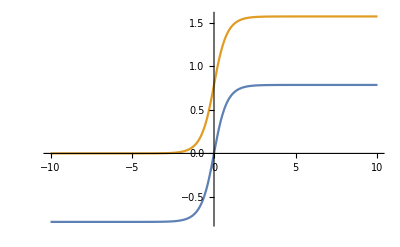

```mathematica
Plot[{f[x], ArcTan[ⅇ^(2 x)]},{x,-10,10}]
```

```mathematica
Abs[f[x]-ArcTan[ⅇ^(2 x)] /.x->0]
```

π/4